b_0 + d_0 = 1, b_1 + c_1 + d_1 = 0, b_0 - b_1 + 3d_0 = 0, -2c_1 + 6d_0 = 0, 2c_1 + 6d_1 =0

WolframAlphaQueryResults

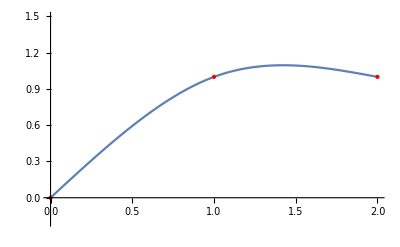

```mathematica
s0[x_]:=(5/4)*x - (1/4)*x^3  (* Replace the right side by the formula for S0. *)
s1[x_]:= 1  + (1/2)*(x-1)-(3/4)*(x-1)^2+(1/4)*(x-1)^3 (* Replace the right side by the formula for S1. *)
plotS0=Plot[s0[x],{x,0,1}];
plotS1=Plot[s1[x],{x,1,2}];
plotPoints=ListPlot[{{0,0},{1,1},{2,1}},PlotStyle->{Red,PointSize[Large]}];
Show[plotS0,plotS1,plotPoints,PlotRange->{{0,2},{-.2,1.5}}]
```

c_0 + d_0 = 0, b_1 + c_1 + d_1 = 0, - b_1 + 2c_0 + 3d_0 = -1, 2c_0 -2c_1 + 6d_0 = 0, b_1 + 2c_1 + 3d_1 =0

WolframAlphaQueryResults

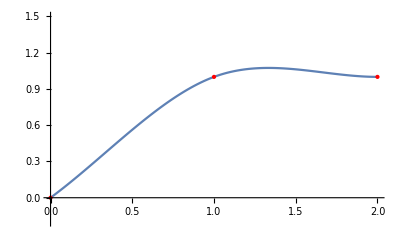

```mathematica
s0[x_]:=x+(1/2)*x^2-(1/2)*x^3  (* Replace the right side by the formula for S0. *)
s1[x_]:= 1  + (1/2)*(x-1)-(x-1)^2+(1/2)*(x-1)^3 (* Replace the right side by the formula for S1. *)
plotS0=Plot[s0[x],{x,0,1}];
plotS1=Plot[s1[x],{x,1,2}];
plotPoints=ListPlot[{{0,0},{1,1},{2,1}},PlotStyle->{Red,PointSize[Large]}];
Show[plotS0,plotS1,plotPoints,PlotRange->{{0,2},{-.2,1.5}}]
```